## Tungsten phonon thermal conductivity

```mathematica
(*/Volumes/MicroSD/Dropbox/PostDoc_SD/W/W_kappaPh_results*)
```

```mathematica
(*important 0.1BMF for ISO is missing - fill it in*)
```

```mathematica
K2meV=0.086173324;
K2eV=K2meV/1000;
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/W/W_kappaPh_results/"];
filePerfW={"bulk/PERF/t_kappa31.dat","100bmf/PERF/t_kappa31.dat","10bmf/PERF/t_kappa31.dat","1bmf/PERF/t_kappa31.dat"};
fileIsoW={"bulk/ISO/t_kappa31.dat", "100bmf/ISO/t_kappa31.dat" ,"10bmf/ISO/t_kappa31.dat","1bmf/ISO/t_kappa31.dat","0.1bmf/ISO/t_kappa31.dat"};
wCondPerf=Table[ReadList[filePerfW[[i]],{Number, Number,Number, Number,Number, Number,Number}],{i,1,filePerfW//Length}];
wCondIso=Table[ReadList[fileIsoW[[i]],{Number, Number,Number, Number,Number, Number,Number}],{i,1,fileIsoW//Length}];
(*"0.1bmf/PERF/t_kappa31.dat", "0.1bmf/ISO/t_kappa31.dat"*)
```

```mathematica
condWperf=Table[Transpose[{Transpose[wCondPerf[[i]]][[1]],Transpose[wCondPerf[[i]]][[2]]}],{i,1,4,1}];
condWiso=Table[Transpose[{Transpose[wCondIso[[i]]][[1]],Transpose[wCondIso[[i]]][[2]]}],{i,1,5,1}];
isoPerfDelta=Table[Transpose[{Transpose[wCondIso[[i]]][[1]],Transpose[wCondPerf[[i]]][[2]]-Transpose[wCondIso[[i]]][[2]]}],{i,1,4,1}];
```

```mathematica
optionsW={AspectRatio->1,FrameLabel->{Style["T (K)",15],Style["κ (W/m/K)",15]},FrameTicksStyle->15,Frame->True,ImageSize->400,PlotLegends->Placed[SwatchLegend[{Style["100000 μm",15],Style["100 μm",15],Style["10 μm",15],Style["1 μm",15],Style["0.1 μm",15]}],{0.85,0.70}],PlotLabel->Style["W phonon conductivity",15],PlotStyle->Thickness[0.007],PlotRange->{{0,3000},{0,500}}};
options2W={AspectRatio->1,FrameLabel->{Style["T (K)",15],Style["κ (W/m/K)",15]},FrameTicksStyle->15,Frame->True,ImageSize->400,PlotLabel->Style["W phonon conductivity",15],PlotStyle->Directive[Thickness[0.007],Dashed],PlotRange->{{0,3000},{0,500}}};
```

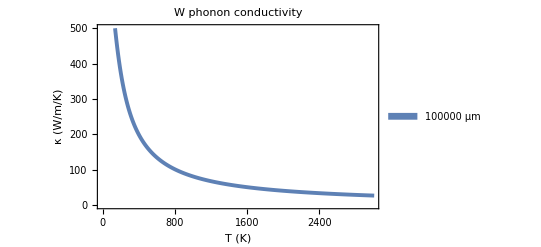

```mathematica
Show[{ListLinePlot[condWperf[[1;;1]],Evaluate[optionsW]]}]
```

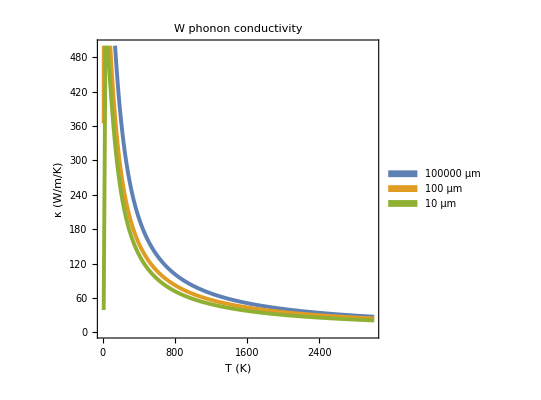

```mathematica
Show[{ListLinePlot[condWperf[[1;;3]],Evaluate[optionsW]]}]
```

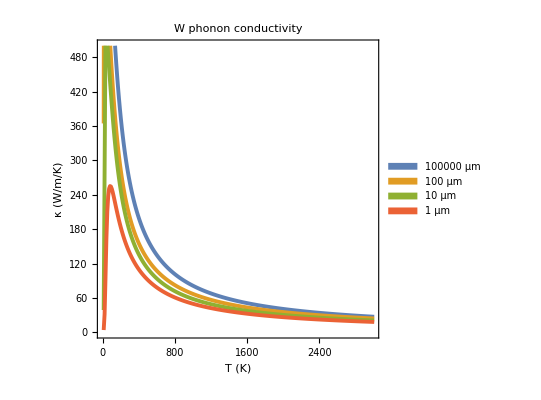

```mathematica
Show[{ListLinePlot[condWperf[[1;;4]],Evaluate[optionsW]]}]
```

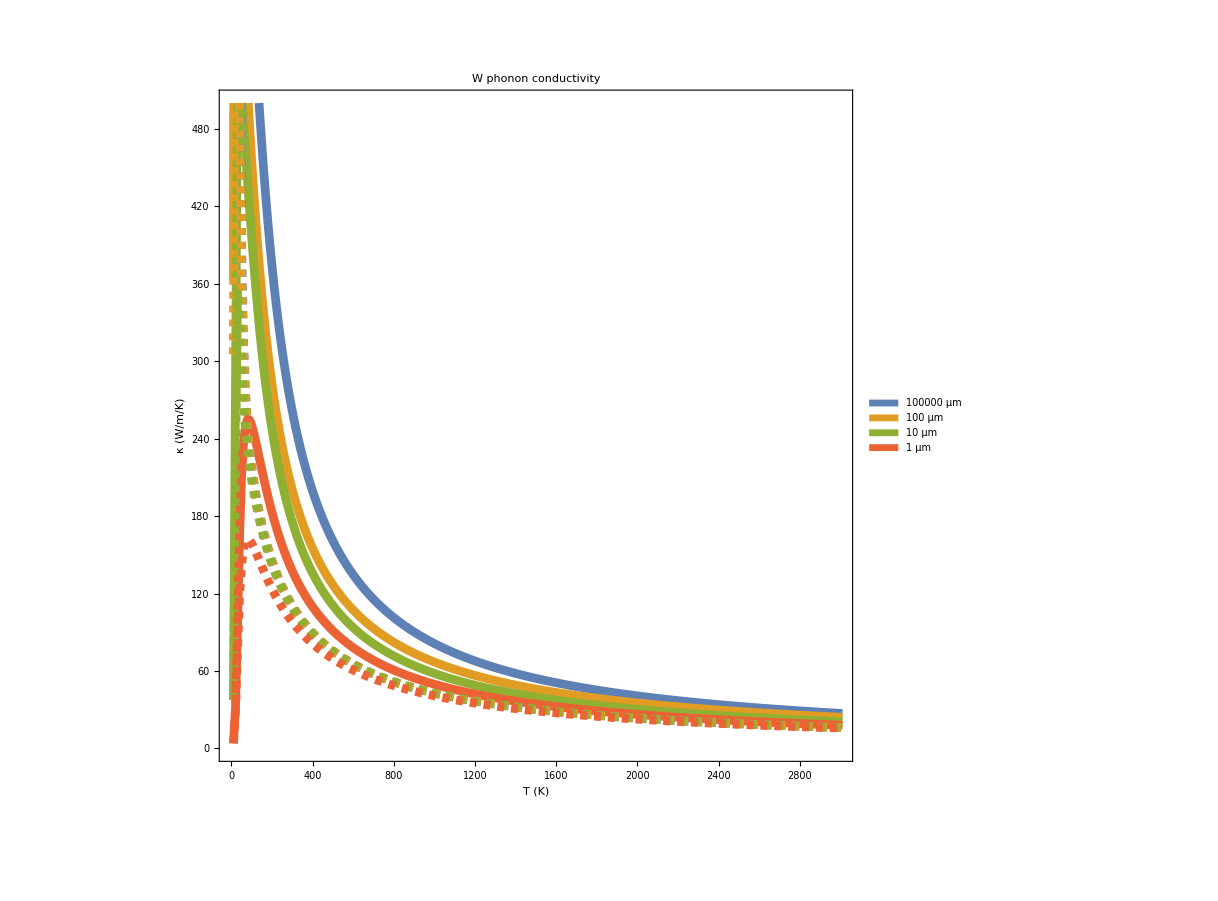

```mathematica
Show[{ListLinePlot[condWperf[[1;;4]],Evaluate[optionsW]],ListLinePlot[condWiso[[1;;4]],Evaluate[options2W]]}]
```

```mathematica
options3W={FrameLabel->{Style["T (K)",15],Style["κ (W/m/K)",15]},FrameTicksStyle->15,Frame->True,ImageSize->400,PlotLegends->Placed[SwatchLegend[{Style["100000 Å",15],Style["100 Å",15],Style["10 Å",15],Style["1 Å",15],Style["0.1 Å",15]}],{0.85,0.70}],PlotLabel->Style["Isotope effect in W phonon conductivity",15],PlotStyle->Thickness[0.007],PlotRange->{{50,1500},{000,500}}};
```

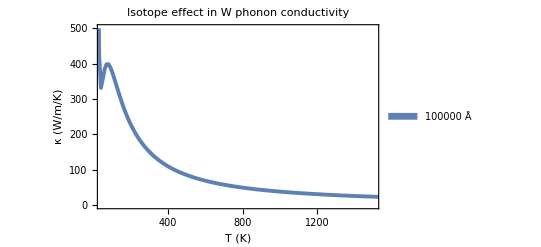

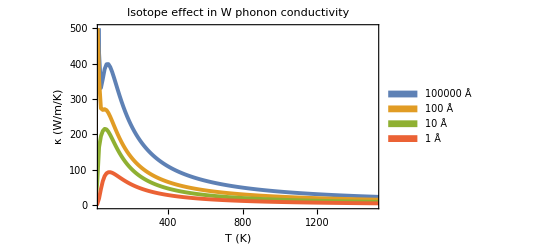

```mathematica
Show[{ListLinePlot[isoPerfDelta[[1;;1]],Evaluate[options3W]]}]
Show[{ListLinePlot[isoPerfDelta[[1;;4]],Evaluate[options3W]]}]
```

```mathematica
w
```